{{x→InterpolatingFunction[{{0., 5.4}}, <>],y→InterpolatingFunction[{{0., 5.4}}, <>],ψ→InterpolatingFunction[{{0., 5.4}}, <>],e_y→InterpolatingFunction[{{0., 5.4}}, <>],e_ψ→InterpolatingFunction[{{0., 5.4}}, <>]}}

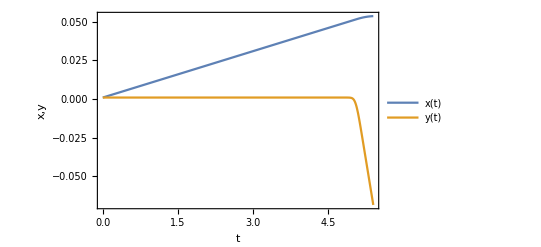

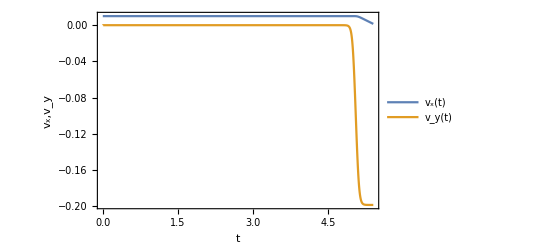

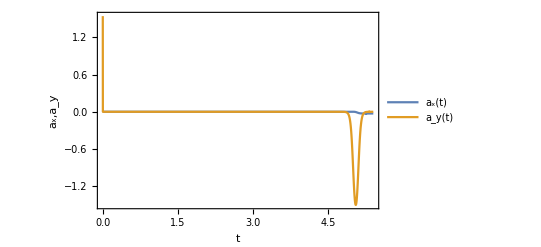

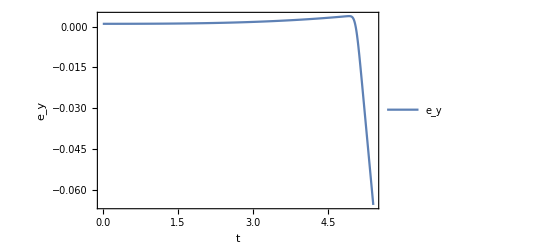

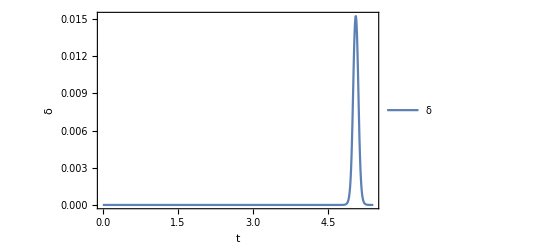

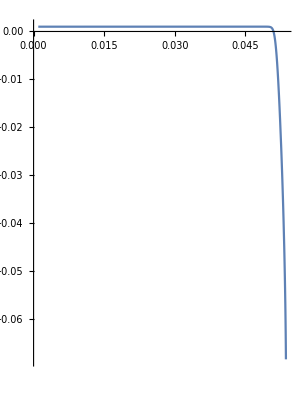

```mathematica
Ratio1[βr_]:=( Sqrt[1.0-βr^2]);
Brake1[t_,τ_,βr_]:=βr*((1+Tanh[20t])/2-(1+Tanh[20(t-τ)])/2);
Brake2[t_,τ0_,τ_,βr_]:=Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
S1[t_,τ1_,δ1_]:=δ1*((1+Tanh[20t])/2-(1+Tanh[20(t-τ1)])/2);
S2[t_,τ01_,τ1_,δ1_]:=Fold[Plus,0,Table[S1[t-τ01⟦k⟧,τ1⟦k⟧,δ1⟦k⟧],{k,1,Length[τ1]}]];
η = Ratio1[(Brake2[t,τ0 ,τ ,Subscript[β, r]])];
δ = S2[t,τ01,τ1,δ1];

Slip angle;
Subscript[α, sl1]=ArcTan[3η*Subscript[μ, 1] Subscript[F, z1]/Subscript[C, α1]]/.rules;Subscript[α, sl2]=ArcTan[3η*Subscript[μ, 2] Subscript[F, z2]/Subscript[C, α2]]/.rules;
Subscript[α, sl3]=ArcTan[3η*Subscript[μ, 3] Subscript[F, z3]/Subscript[C, α3]]/.rules;Subscript[α, sl4]=ArcTan[3η*Subscript[μ, 4] Subscript[F, z4]/Subscript[C, α4]]/.rules;

Subscript[α, 1]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-δ/.rules;
Subscript[α, 2]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])-δ/.rules;Subscript[α, 3]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])/.rules;Subscript[α, 4]=((y'[t] + Subscript[l, f] ψ'[t])/x'[t])/.rules;

Tire  Force;
Subscript[f, y1]=Piecewise[{{ -Subscript[C, α1]Tan[Subscript[α, 1]]+ ((Subscript[C, α1])^2/(3η*Subscript[μ, 1] Subscript[F, z1]) Abs[Tan[Subscript[α, 1]]] Tan[Subscript[α, 1]])- ((Subscript[C, α1])^3/(27(η Subscript[μ, 1] Subscript[F, z1])^2)(Tan[Subscript[α, 1]])^3),(Abs[Subscript[α, 1]])<Subscript[α, sl1]},{-η Subscript[μ, 1] Subscript[F, z1] Sign[Subscript[α, 1]],(Abs[Subscript[α, 1]])≥Subscript[α, sl1]}}]/.rules;
Subscript[f, y2]=Piecewise[{{ -Subscript[C, α2] Tan[Subscript[α, 2]]+ ((Subscript[C, α2])^2/(3η*Subscript[μ, 2] Subscript[F, z2]) Abs[Tan[Subscript[α, 2]]] Tan[Subscript[α, 2]])- ((Subscript[C, α2])^3/(27(η Subscript[μ, 2] Subscript[F, z2])^2)(Tan[Subscript[α, 2]])^3),(Abs[Subscript[α, 2]])<Subscript[α, sl2]},{-η Subscript[μ, 2] Subscript[F, z2] Sign[Subscript[α, 2]],(Abs[Subscript[α, 2]])≥Subscript[α, sl2]}}]/.rules;
Subscript[f, y3]=Piecewise[{{-Subscript[C, α3] Tan[Subscript[α, 3]]+ ((Subscript[C, α3])^2/(3η*Subscript[μ, 3] Subscript[F, z3]) Abs[Tan[Subscript[α, 3]]] Tan[Subscript[α, 3]])- ((Subscript[C, α3])^3/(27(η Subscript[μ, 3] Subscript[F, z3])^2)(Tan[Subscript[α, 3]])^3),(Abs[Subscript[α, 3]])<Subscript[α, sl3]},{ -η Subscript[μ, 3] Subscript[F, z3] Sign[Subscript[α, 3]],(Abs[Subscript[α, 3]])≥Subscript[α, sl3]}}]/.rules;
Subscript[f, y4]=Piecewise[{{-Subscript[C, α4] Tan[Subscript[α, 4]]+ ((Subscript[C, α4])^2/(3η*Subscript[μ, 4] Subscript[F, z4]) Abs[Tan[Subscript[α, 4]]] Tan[Subscript[α, 4]])- ((Subscript[C, α4])^3/(27(η Subscript[μ, 4] Subscript[F, z4])^2)(Tan[Subscript[α, 4]])^3),(Abs[Subscript[α, 4]])<Subscript[α, sl4]},{-η Subscript[μ, 4] Subscript[F, z4] Sign[Subscript[α, 4]],(Abs[Subscript[α, 4]])≥Subscript[α, sl4]}}]/.rules;

Subscript[F, x1] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 1] Subscript[F, z1] Cos[δ] - Subscript[f, y1] Sin[δ]/.rules;
Subscript[F, x2] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 2] Subscript[F, z2] Cos[δ] - Subscript[f, y2] Sin[δ]/.rules;
Subscript[F, x3] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 3] Subscript[F, z3] Cos[0] - Subscript[f, y3] Sin[0]/.rules;
Subscript[F, x4] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 4] Subscript[F, z4] Cos[0] - Subscript[f, y4] Sin[0]/.rules;

Subscript[F, y1] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 1] Subscript[F, z1] Sin[δ] + Subscript[f, y1] Cos[δ]/.rules;
Subscript[F, y2] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 2] Subscript[F, z2] Sin[δ] + Subscript[f, y2] Cos[δ]/.rules;
Subscript[F, y3] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 3] Subscript[F, z3] Sin[0] + Subscript[f, y3] Cos[0]/.rules;
Subscript[F, y4] =(Brake2[t,τ0,τ,Subscript[β, r]])*Subscript[μ, 4] Subscript[F, z4] Sin[0] + Subscript[f, y4] Cos[0]/.rules;

Eq1 = m D[x[t],{t,2}] == m D[y[t],{t,1}]D[ψ[t],{t,1}] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4]/.rules;
Eq2 = m D[y[t],{t,2}] == -m D[x[t],{t,1}] D[ψ[t],{t,1}] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4]/.rules; 
Eq3 =Subscript[J, z] D[ψ[t],{t,2}] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r]*(Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)(-Subscript[F, x1] + Subscript[F, x2] - Subscript[F, x3] + Subscript[F, x4])/.rules;
Eq4 = m D[Subscript[e, ψ][t],{t,1}]==m D[ψ[t],{t,1}]-m D[Subscript[ψ, d][t],{t,1}]/.rules;
Eq5 = m D[Subscript[e, y][t],{t,1}]==m D[y[t],{t,1}] Cos[Subscript[e, ψ][t]] + m D[x[t],{t,1}]Sin[Subscript[e, ψ][t]]/.rules;
rules =
{
Subscript[C, α1]->80000.0,Subscript[C, α2]->80000.0,Subscript[C, α3]->80000.0,Subscript[C, α4]->80000.0,
Subscript[μ, 1]->1.0,Subscript[μ, 2]->1.0,Subscript[μ, 3]->1.0,Subscript[μ, 4]->1.0,
Subscript[F, z1]->26719.0,Subscript[F, z2]->26719.0,Subscript[F, z3]->21295.0,Subscript[F, z4]->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
(*Tune Subscript[K, y],Subscript[K, ψ],Subscript[t, lp],Subscript[ψ, d1]*)
Subscript[K, y]->0,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};

time =5.4;

τ0 = {0,10,20,50};
τ = {5,5,5,5};
Subscript[β, r]={0,0.5,-0.5,0.6};

τ01 = {5,8,19,102,135 ,140};
τ1 = {0.1,4,39,4,3 ,20};
δ1={0.02,-0.023,0.025,0.02,-0.025,0.025};

Subscript[ψ, d][t]=ArcCos[x[t]^2/( Subscript[t, lp] Sqrt[D[x[t],t]^2+D[y[t],t]^2])]/.rules;


initCond={x[0]==0.001,x'[0]==0.01,y[0]==0.001,y'[0]==-0.0001,ψ[0]==0.001,ψ'[0]==0,Subscript[e, y][0]==0.001,Subscript[e, ψ][0]==0.001};

solution=NDSolve[{Eq1,Eq2,Eq3,Eq4,Eq5,initCond},{x,y,ψ,Subscript[e, y],Subscript[e, ψ]},{t,0,time}]

Plot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","x,y"},PlotLegends->{"x(t)","y(t)"},PlotRange->All] 
Plot[Evaluate[{x'[t],y'[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","v_x,v_y"},PlotLegends->{"v_x(t)","v_y(t)"},PlotRange->All] 
Plot[Evaluate[{x''[t],y''[t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","a_x,a_y"},PlotLegends->{"a_x(t)","a_y(t)"},PlotRange->All] 
Plot[Evaluate[{Subscript[e, y][t]}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","e_y"},PlotLegends->{"e_y"},PlotRange->All] 
Plot[Evaluate[{δ}/.solution],{t,0,time},Frame->True,FrameLabel->{"t","δ"},PlotLegends->{"δ"},PlotRange->All]
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,time},PlotRange-> All]
```

```mathematica
.
```